```mathematica
Bracket[this_]:=DisplayForm[StyleBox[RowBox[{"[", this,"]"}],SpanMaxSize->Infinity]]
```

```mathematica
Graph[CycleGraph[5],ImageSize->50, VertexSize->Large]
```

-Graphics-

```mathematica
Bracket[Graph[EdgeAdd[CycleGraph[5],{5<->3,5<->2}],ImageSize->20, VertexSize->Large]]
```

Bracket[-Graphics-]

```mathematica
AddEdge[g_,edges_]:=Graph[EdgeAdd[g,edges], EdgeStyle->Table[e->{Thick,Darker[Green]},{e,edges}]]
```

```mathematica
AddEdge[g_,edges_, edges2_]:=Graph[EdgeAdd[g,Join[edges2,edges]], EdgeStyle->Join[Table[e->{Thick,Red},{e,edges2}],Table[e->{Thick,Darker[Green]},{e,edges}]]]
```

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{
CycleGraph[4],
Graph[CycleGraph[4],VertexStyle->{ 1 -> Red}],
Graph[CycleGraph[4],VertexStyle->{ 2 -> Red}],
AddEdge[CycleGraph[4],{1<->3}],
Graph[AddEdge[CycleGraph[4],{1<->3}],VertexStyle->{ 3 -> Red}],
AddEdge[CycleGraph[4],{2<->4}],
Graph[AddEdge[CycleGraph[4],{2<->4}],VertexStyle->{ 4 -> Red}],
Graph[AddEdge[CycleGraph[4],{1<->5,2<->5,3<->5,4<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[AddEdge[CycleGraph[4],{1<->5,2<->5,3<->5},{4<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[AddEdge[CycleGraph[4],{1<->5,2<->5,3<->5},{}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[AddEdge[CycleGraph[4],{1<->5,2<->5},{3<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[AddEdge[CycleGraph[4],{1<->5},{2<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[AddEdge[CycleGraph[4],{},{1<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[VertexAdd[CycleGraph[4],5], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}]
}
],FrameMargins->20, Frame->True
]
```

[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{
CompleteGraph[5],
CompleteGraph[4],
Graph[AddEdge[CycleGraph[3],{1<->4,2<->4,3<->4}],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
Graph[AddEdge[CycleGraph[3],{1<->4,2<->4},{3<->4}],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
Graph[AddEdge[CycleGraph[3],{1<->4,2<->4}],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
Graph[AddEdge[CycleGraph[3],{1<->4},{2<->4}],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
Graph[AddEdge[CycleGraph[3],{},{1<->4}],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
Graph[VertexAdd[CycleGraph[3],4],VertexCoordinates->Join[circleLayout[3],{{0,0}}]],
CompleteGraph[3],
CycleGraph[5],
Graph[AddEdge[CycleGraph[5],{1<->6,2<->6,3<->6,4<->6,5<->6}],VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
AddEdge[CycleGraph[5],{5<->3,5<->2}],
AddEdge[CycleGraph[5],{4<->1,4<->2}],
AddEdge[CycleGraph[5],{3<->1}],
AddEdge[CycleGraph[5],{1<->3,1<->4}],
AddEdge[CycleGraph[5],{4<->2}],
AddEdge[CycleGraph[5],{5<->3,5<->2},{4<->1,4<->2}],
AddEdge[CycleGraph[5],{4<->1,4<->2},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{3<->1},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{3<->1},{4<->1,4<->2}],
AddEdge[CycleGraph[5],{1<->3,1<->4},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{4<->2},{1<->3,1<->4,5<->3,5<->2}],
CycleGraph[4],
AddEdge[CycleGraph[4],{1<->3}],
AddEdge[CycleGraph[4],{2<->4}],
Graph[AddEdge[CycleGraph[4],{1<->5,2<->5,3<->5,4<->5}], VertexCoordinates->{{0,10},{10,0},{20,10},{10,20},{10,10}}],
Graph[VertexContract[CycleGraph[4],{2,4}],VertexStyle->{2->Red}],
Graph[EdgeAdd[VertexContract[CycleGraph[4],{2,4}],{2<->2}],VertexStyle->{2->Red}]
}
],FrameMargins->20, Frame->True
]
```

[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]

```mathematica
AddEdge2[g_,edges_]:=Graph[EdgeAdd[g,edges], EdgeStyle->Table[e->{Thick,DotDashed,Blue},{e,edges}]]
```

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{

AddEdge2[CycleGraph[5],{5<->3}],
AddEdge2[CycleGraph[5],{3<->1,4<->2}],
AddEdge2[CycleGraph[5],{3<->5,4<->2}],
AddEdge2[CycleGraph[5],{2<->5,4<->1}],
AddEdge2[CycleGraph[5],{1<->4,3<->5}],
AddEdge2[CycleGraph[5],{1<->3,2<->5}],
AddEdge2[CycleGraph[5],{1<->3}],
AddEdge2[CycleGraph[5],{1<->4}],
AddEdge2[CycleGraph[5],{5<->2}],
AddEdge2[CycleGraph[5],{5<->3,5<->2}],
AddEdge2[CycleGraph[5],{4<->1,4<->2}],
AddEdge2[CycleGraph[5],{3<->1}],
AddEdge2[CycleGraph[5],{1<->3,1<->4}],
AddEdge2[CycleGraph[5],{4<->2}],
AddEdge[CycleGraph[5],{5<->3,5<->2},{4<->1,4<->2}],
AddEdge[CycleGraph[5],{4<->1,4<->2},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{3<->1},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{3<->1},{4<->1,4<->2}],
AddEdge[CycleGraph[5],{1<->3,1<->4},{5<->3,5<->2}],
AddEdge[CycleGraph[5],{4<->2},{1<->3,1<->4,5<->3,5<->2}],

}
],FrameMargins->20, Frame->True
]
```

[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[Graph[Graph[Null,ImageSize→40,VertexSize→Medium]]]

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{

Graph[AddEdge[CycleGraph[5],{1<->6,2<->6,3<->6,4<->6},{5<->6}],VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{1<->6,2<->6,3<->6},{4<->6}],VertexStyle->{5->Red}, VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{5<->3,5<->2},{}],VertexStyle->{5->Red}, VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{1<->6,2<->6},{3<->6}],VertexStyle->{4->Red}, VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{4<->1,4<->2},{}],VertexStyle->{4->Red}, VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{1<->6},{2<->6}],VertexStyle->{3->Red}, VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{1<->3},{}],VertexStyle->{3->Red}, VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{},{}],VertexStyle->{2->Red}, VertexCoordinates->circleLayout[5]],
Graph[VertexAdd[CycleGraph[5],6], VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{},{1<->6}],VertexStyle->{1->Red}, VertexCoordinates->Join[circleLayout[5],{{0,0}}]],
Graph[AddEdge[CycleGraph[5],{},{}],VertexStyle->{1->Red}, VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{},{}], VertexCoordinates->circleLayout[5]]
}
], Frame->True
]
```

[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]

```mathematica
Flatten[Table[i<->j->Green,{i,1,5}{j,1,5}]]
```

{i<->j→RGBColor[0, 1, 0],i<->j→RGBColor[0, 1, 0],i<->j→RGBColor[0, 1, 0]}

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{

Graph[CompleteGraph[5], EdgeStyle->Flatten[Table[i<->j->Darker[Green],{i,1,5},{j,1,5}]]]
}
], Frame->True
]
```

[-Graphics-]

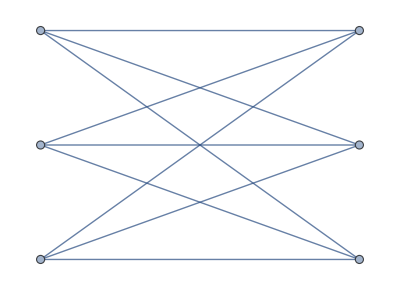

```mathematica
CompleteGraph[{3,3}]
```

```mathematica
Column[
Map[Bracket[Graph[Graph[#,ImageSize->40, VertexSize->Medium]]]&,
{

Graph[AddEdge[CycleGraph[5],{5<->3,5<->2},{1<->3,1<->4,2<->4}], VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{2<->4,1<->4},{5<->3,5<->2,1<->3}], VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{1<->3},{5<->3,5<->2,2<->4,1<->4}], VertexCoordinates->circleLayout[5]],


Graph[AddEdge[CycleGraph[5],{1<->3,1<->4,2<->4},{5<->3,5<->2}], VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{5<->3,5<->2,1<->3},{2<->4,1<->4}], VertexCoordinates->circleLayout[5]],
Graph[AddEdge[CycleGraph[5],{5<->3,5<->2,2<->4,1<->4},{1<->3}], VertexCoordinates->circleLayout[5]],
CompleteGraph[5]
}
], Frame->True
]
```

[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]
[-Graphics-]

```mathematica
circleLayout[n_]:=Table[{Cos[2π/n i+Pi/2],Sin[2π/n i+Pi/2]},{i,n}]
```

```mathematica
circleLayout2[n_]:=Table[{Cos[2π/n i+4Pi/5],Sin[2π/n i+4Pi/5]},{i,n}]
```

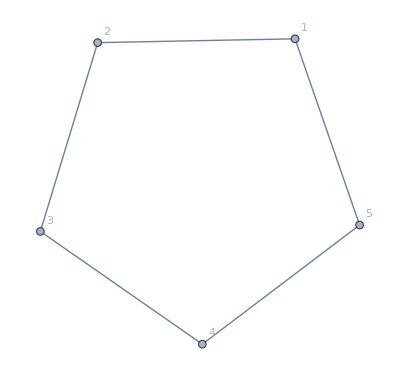

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1}, VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Take[deps2,-1]
```

{{20,38,{2,3<->6,2<->4}}}

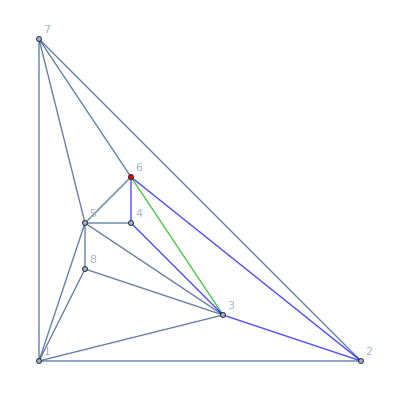

```mathematica
Graph[ReadGrof[20], GraphLayout->"PlanarEmbedding",VertexLabels->"Name",
EdgeStyle->{3<->6->{Thick,Darker[Green]}, 3<->4->{Thick,Blue}, 6<->4->{Thick,Blue}, 6<->2->{Thick,Blue}, 3<->2->{Thick,Blue}},
VertexStyle->{6->Red}]
```

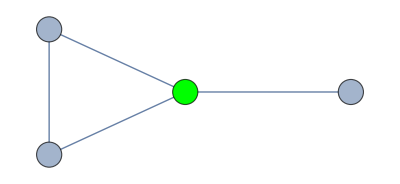

```mathematica
Graph[{1<->2,2<->3,3<->1,3<->4}, VertexStyle->{3 -> Green},VertexSize->Medium]
```

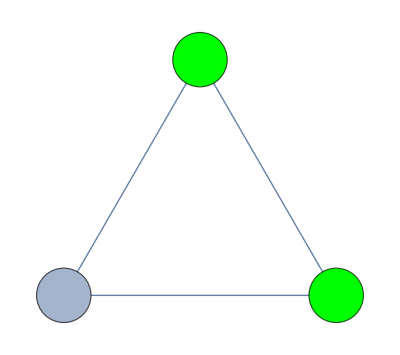



```mathematica
Graph[VertexContract[VertexContract[CycleGraph[5],{3,1}],{4,2}], VertexStyle->{4->Green,3 -> Green},VertexSize->Medium]
```

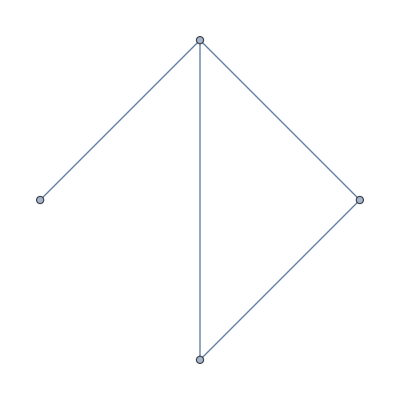

```mathematica
VertexContract[CycleGraph[5],{3,1}]
```

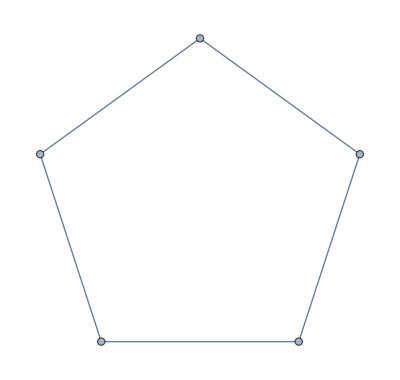

```mathematica
VertexContract[Graph[{1<->2,2<->3,3<->4,4<->5,5<->1}],3<->1]
```

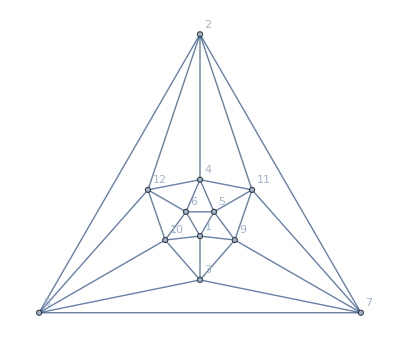

```mathematica
Graph[GraphData["IcosahedralGraph"], VertexLabels->"Name"]
```

```mathematica
'
```

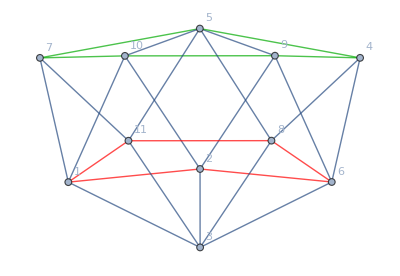

```mathematica
Graph[ReadGrof[897], GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name", 
EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[{1,2,6,8,11}]],
Map[#->Darker[Green]&,Rule3Cycle[{7,10,9,4,5}]]
]
]
```

```mathematica
EdgeList[GraphData["IcosahedralGraph"]]
```

{1<->3,1<->5,1<->6,1<->9,1<->10,2<->4,2<->7,2<->8,2<->11,2<->12,3<->7,3<->8,3<->9,3<->10,4<->5,4<->6,4<->11,4<->12,5<->6,5<->9,5<->11,6<->10,6<->12,7<->8,7<->9,7<->11,8<->10,8<->12,9<->11,10<->12}

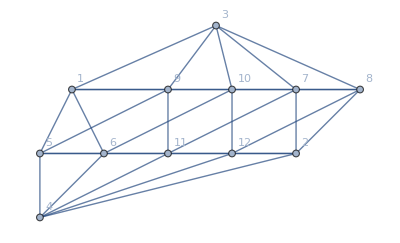

```mathematica
Graph[{1<->3,1<->5,1<->6,1<->9,1<->10,2<->4,2<->7,2<->8,2<->11,2<->12,3<->7,3<->8,3<->9,3<->10,4<->5,4<->6,4<->11,4<->12,5<->6,5<->9,5<->11,6<->10,6<->12,7<->8,7<->9,7<->11,8<->10,8<->12,9<->11,10<->12}, GraphLayout->"LayeredEmbedding", VertexLabels->"Name"

]
```

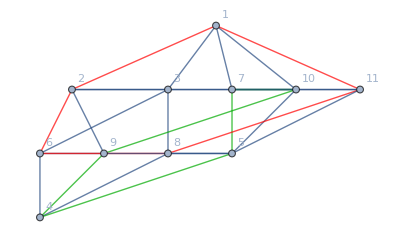

```mathematica
Graph[ReadGrof[897], GraphLayout->"LayeredEmbedding", VertexLabels->"Name", 
EdgeStyle->
Join[
Map[#->Red&,Rule3Cycle[{1,2,6,8,11}]],
Map[#->Darker[Green]&,Rule3Cycle[{7,10,9,4,5}]]
]
]
```

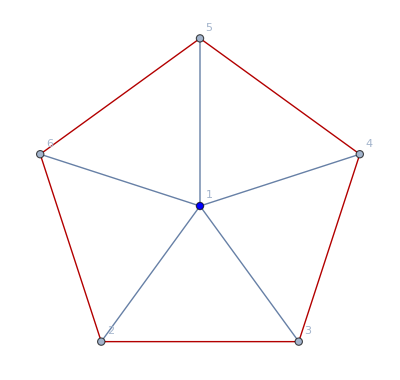

```mathematica
Graph[WheelGraph[6],VertexLabels->"Name",GraphHighlight->Rule3Cycle[{6,2,3,4,5}], VertexStyle->{1 -> Blue}]
```

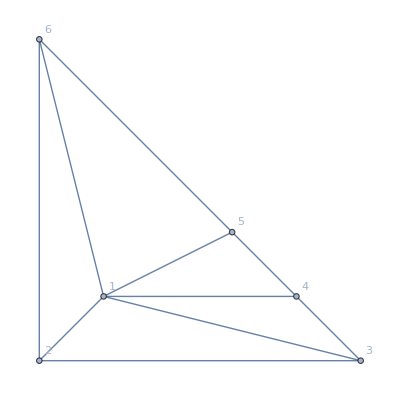

```mathematica
Graph[WheelGraph[6],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

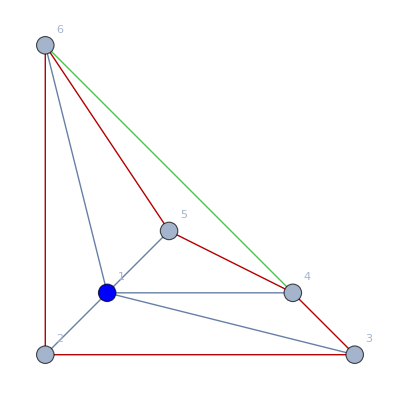

```mathematica
Graph[EdgeAdd[WheelGraph[6],6<->4],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlight->Rule3Cycle[{6,2,3,4,5}], VertexStyle->{1 -> Blue}, VertexSize->Medium, EdgeStyle->{4<->6->Darker[Green]}]
```

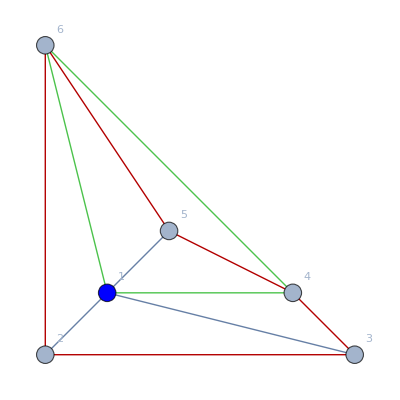

```mathematica
Graph[EdgeAdd[WheelGraph[6],6<->4],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", GraphHighlight->Rule3Cycle[{6,2,3,4,5}], VertexStyle->{1 -> Blue}, VertexSize->Medium, EdgeStyle->{4<->6->{Thick,Darker[Green]},4<->1->{Thick,Darker[Green]},1<->6->{Thick,Darker[Green]}}]
```

```mathematica
Map[Last,ToColors2[<|x1->1,x2->2,x3->1,x4->2,x5->3|>]]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

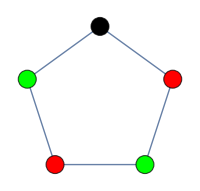
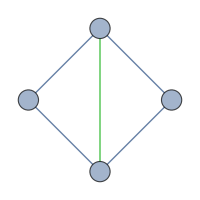

```mathematica
Map[Graph[#,ImageSize->200,VertexSize->Medium]&,
{
Graph[CycleGraph[5],VertexStyle->{1 -> Green, 3 -> Green, 5->Black, 4->Red,2->Red}, VertexSize->Large],
AddEdge[CycleGraph[4],{2<->4}]
}
]
```